Misschien het verbruik nog veranderen naar km/l en km/kWh

## Totaal Model Energieverlies Transport

### Definities

#### Tekstopmaak

```mathematica
b[string_]:=Style[string,FontWeight->Bold,Red]
tekstrood[tekst_]:=TextCell[Style[tekst, FontSize->18,FontFamily->"Georgia",Red]];
tekst[tekst_,size_:18]:=TextCell[Style[tekst, FontSize->size,FontFamily->"Georgia",Black]];
tekstb[tekst_,size_:18]:=TextCell[Style[tekst, FontSize->size,FontFamily->"Georgia",FontWeight->Bold,Black]];
tekstkleur[tekst_,kleur_,size_:18]:=TextCell[Style[tekst, FontSize->size,FontFamily->"Georgia",kleur]];
```

#### Snelheidomzetter

```mathematica
m2km[lijst_]:=({#[[1]],#[[2]]*3.6})&/@lijst (*Zet een lijst met {[s], [m/s]} om naar {[s], [km/h]}*);
km2m[lijst_]:=({#[[1]],#[[2]]/3.6})&/@lijst (*Zet een lijst met {[s], [km/h]} om naar {[s], [m/s]}*);
```

#### Integreerder

```mathematica
integreerder[lijst_]:=Module[{l,input,output,cumopp,cumopplist,dti,hs,os,ht,ot,oi},
l=Length[lijst];
input=0;
output=0;
cumopp=0;
cumopplist={lijst[[1]]};
For[i=1,i<l,i++,
dti=lijst[[i+1,1]]-lijst[[i,1]];
(*Gives time interval between point i and point i+1 (in s)*)
hs=lijst[[i,2]];
(*Gives the hight of the square part belonging to interval dti *)
os=dti*hs;
(*Gives the surface area of the square part*)
ht=lijst[[i+1,2]]-lijst[[i,2]];
(*Hight of the triangular part*)
ot=(1/2)*dti*ht;
(*Surface area of the triangular part*)
oi=os+ot;
(*Surface area per interval*)
If[oi<0,output+=oi,input+=oi];
(*For negative oi, the surface area is added to output. Otherwise it's addedto the input*)
cumopp+=oi;
(*Updates cumulative surface area*)
If[dti≠0,cumopplist=Append[cumopplist,{lijst[[i+1,1]],cumopp}]]
(*Adds the latest cumopp to the cumopplist list but only if dti ≠ 0*)
];
{input,output}];
```

```mathematica
integreerder[NEDC]*1000/3600
```

{2999.54,0}

```mathematica
32395./3
```

10798.3

#### NEDC Parcour

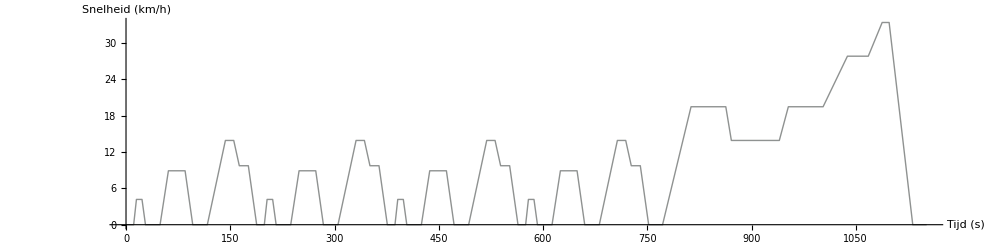

```mathematica
ECEdeel1={{0,0},{11,0},{15,15},{23,15},{28,0},{49,0},{61,32},{85,32},{96,0},{117,0},{143,50},{155,50},{163,35},{176,35}};
ECEdeel2=({#[[1]]+188,#[[2]]})&/@ECEdeel1;
ECEdeel3=({#[[1]]+188,#[[2]]})&/@ECEdeel2;
ECEdeel4=({#[[1]]+188,#[[2]]})&/@ECEdeel3;
EUDC0={{0,0},{20,0},{61,70},{111,70},{119,50},{188,50},{201,70},{251,70},{286,100},{316,100},{336,120},{346,120},{380,0},{400,0}};
EUDC=({#[[1]]+752,#[[2]]})&/@EUDC0;
NEDC=km2m[Join[ECEdeel1,ECEdeel2,ECEdeel3,ECEdeel4,EUDC]];(*NEDC parcour data met tijd in seconden en snelheid in m/s*)
NEDCsimple=km2m[Join[ECEdeel1,({#[[1]]+188,#[[2]]})&/@EUDC0]];(*NEDC parcour data met tijd in seconden en snelheid in m/s*)
NEDCs=integreerder[NEDC][[1]];(*Totale afstand NEDC parcour in meter*)
NEDCt=NEDC[[-1,1]];(*Totale tijd NEDC parcour in seconden*)
NEDCvavg=NEDCs/(NEDCt-5);(*Gemiddelde snelheid NEDC parcour in m/s, rekening houdend met 5 seconde opstarten en remmen*)
NEDCavg={{0,0},{5,NEDCvavg},{NEDCt-5,NEDCvavg},{NEDCt,0}};(*Zelfde afstand en tijd als het NEDC parcour maar nu met de gemiddelde snelheid (in m/s)*)
ListLinePlot[{NEDC},AxesLabel->{"Tijd (s)","Snelheid (km/h)"},PlotStyle->grijs,ImageSize->IS,AspectRatio->AR,LabelStyle->LS]
```

#### Overige Parcours

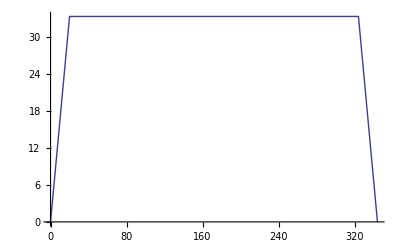

```mathematica
ECOhoog={{0,0},{20,120/3.6},{324,120/3.6},{344,0}};
ECO={{0,0},{10,25/3.6},{1555,25/3.6},{1565,0}};
AmsterdamUtrecht={{0,0},{10,10},{20,0},{50,0},{80,7},{150,12},{300,10},{600,16},{610,0},{700,0},{800,12},{810,13},{1300,20},{1310,25},{1900,25},{1910,30},{2100,30},{2120,27},{2300,25},{2350,25},{2360,20},{2500,20},{2510,10},{2600,10},{2630,15},{2690,10},{2700,0}};
ListLinePlot[ECOhoog]
```

### Remverlies (RemVerlies)

```mathematica
RemVerlies[vlijst_,m_]:=Module[{v,a,Pr},
v=Interpolation[vlijst,InterpolationOrder->1];
a=v';
Pr[t_]:=m*a[t]*v[t];
Plot[{v[t],a[t],Pr[t]},{t,0,vlijst[[-1,1]]}]
]
```

```mathematica
Remverlies[NEDC,1];
```

### Lucht- en Rolwrijving (LuchtRol)

```mathematica
LuchtRol[vlijst_,m_:1600,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3]:=Module[{ρ,g,v,Pwl,Pwr,Ptot},
ρ=1.225;
g=9.81;
v=Interpolation[vlijst,InterpolationOrder->1];
Pwl[t_]:=1/2 A*ρ*cd*v[t]^3;
Pwr[t_]:=m*crr*g*v[t];
Ptot[t_]:=Pwl[t]+Pwr[t];
Plot[{v[t],Pwl[t],Pwr[t],Ptot[t]},{t,0,vlijst[[-1,1]]}]
]
```

```mathematica
LuchtRol[NEDC];
```

### Remverlies samen met Lucht- en Rolwrijving (RemLuchtRol)

#### Grafiekinstellingen

```mathematica
padding={{60,60},{30,60}}(*Set padding voor de grafieken, nodig om uitlijning goed te krijgen*);
IS=1000;
AR=1/4;
LS=Directive[FontFamily->"Georgia",FontSize->14];
GL=Automatic;
GLS=Lighter[Gray,0.6];

RGB[r_,g_,b_]:=RGBColor[r/255,g/255,b/255];
blauw=RGB[59,108,157];
groen=RGB[110,164,90];
paars=RGB[131,81,140];
grijs=RGB[143,146,145];
rood=RGB[202,66,62];
OP=0.1;
Clucht=blauw; CluchtF=Opacity[OP,Clucht];
Crol=grijs;CrolF=Opacity[OP,Crol];
Crem=paars;CremF=Opacity[OP,Crem];
Ctot=groen;CtotF=Opacity[OP,Ctot];
CTOT=rood;CTOTF=Opacity[OP,CTOT];

BeschrijvingSE[Stot_,Etot_,ETOT_]:=
Row[{
tekst["De afgelegde weg is "],
tekstb[ToString[Round[Stot/1000,0.1]]<>" kilometer"],
tekst[", het brandstofgebruik is "],
tekstkleur[ToString[Round[ETOT/10^6,0.01]]<>" MJ",CTOT],
tekst[", en er gaat "],
tekstkleur[ToString[Round[Etot/10^6,0.01]]<>" MJ",Ctot],
tekst[" verloren in de aandrijving."]}];
BeschrijvingSE0=Row[{
tekst["Updaten… "]}];

BeschrijvingOLR[Otot_,Ltot_,Rtot_]:=
Row[{
tekstkleur["(hiervan is ",RGBColor[0,0,0,0.3]],
tekstkleur[ToString[Round[Otot/10^6,0.01]]<>" MJ optrekenergie",Crem],
tekstkleur[", ",RGBColor[0,0,0,0.3]],
tekstkleur[ToString[Round[Ltot/10^6,0.01]]<>" MJ luchtwrijving",Clucht],
tekstkleur[", en ",RGBColor[0,0,0,0.3]],
tekstkleur[ToString[Round[Rtot/10^6,0.01]]<>" MJ rolwrijving",Crol],
tekstkleur[")",RGBColor[0,0,0,0.3]]}];
BeschrijvingOLR0=
Row[{
tekstkleur["(...)",RGBColor[0,0,0,0.3]]}];
```

#### Code

```mathematica
RemLuchtRol[vlijst_,ma_:1600,mb_:30,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3,RR_:0,EV_:False,auto_:"VW Passat"]:=Module[{ρ,g,ti,tf,m,EnergieInhoud,v,a,Pro,Prr,Pwl,Pwr,Ptot,PTOT,Stot,Otot,Ltot,Rtot,Etot,verliezen,ETOT,mpJ,Bereik,GebruikkWh,GebruikL,fracties,label,labelmaker,vtPlot,PrPlot,PwrPlot,PwlPlot,PtotPlot,PTOTPlot,BarPlot,WegEnVerbruik,BereikTekst,tabview1,tabview2,AutoKeuze},

(*CONSTANTEN*)

ρ=1.225;
g=9.81;
ti=vlijst[[1,1]];
tf=vlijst[[-1,1]];
m=ma+mb;
EnergieInhoud=If[EV,
mb*0.6*10^6,(*Gebaseerd op Litium-ion: 0,36-0,875 MJ/kg*)
mb*46*10^6 (*Gebaseerd op Benzine: 46 MJ/kg*)
];

(*BEWEGINGS-VERGELIJKINGEN*)

v=Interpolation[vlijst,InterpolationOrder->1];
a=v';
Pro[t_]:=If[a[t]>=0,(1-RR)m*a[t]*v[t],0];(*De "1-RR" factor bepaalt hier hoeveel in hoeverre regeneratief remmen energie bespaart*)
Prr[t_]:=If[a[t]<=0,(1-RR)m*a[t]*v[t],Null];
Pwl[t_]:=1/2 A*ρ*cd*v[t]^3;
Pwr[t_]:=m*crr*g*v[t];
Ptot[t_]:=Pwl[t]+Pwr[t]+Pro[t];
PTOT[t_]:=Ptot[t]/η;

(* INTGRALEN *)

Stot=NIntegrate[v[t],{t,ti,tf}];
Otot=NIntegrate[Pro[t],{t,ti,tf}];
Ltot=NIntegrate[Pwl[t],{t,ti,tf}];
Rtot=NIntegrate[Pwr[t],{t,ti,tf}];
Etot=NIntegrate[Ptot[t],{t,ti,tf}];
ETOT=Etot/η;
verliezen={ETOT-Etot,Otot,Ltot,Rtot};(*Verliezen per onderdeel, in Joule*)

(* BEREIK & GEBRUIK *)

mpJ=Stot/ETOT;(* Verbruik in meter per Joule *)
Bereik=EnergieInhoud*mpJ;
GebruikkWh=mpJ*(3.6*10^6)/10^3(*Omrekenen van meter/Joule naar km/kWh*);
GebruikL=mpJ*(34.3*10^6)/10^3(*Omrekenen van meter/Joule naar km/(liter benzine)*);
fracties[lijst_]:=({#*GebruikkWh,#*GebruikL})&/@(lijst/Total[lijst]);
label[kWh_,L_]:=Text[Grid[{{Round[kWh,0.1],"km/kWh"},{Round[L,0.1],"km/L"}},Alignment->"/"]];
labelmaker[lijst_]:=Table[Tooltip[lijst[[i]],label[fracties[lijst][[i,1]],fracties[lijst][[i,2]]]],{i,1,Length[lijst]}];

(*GRAFIEKEN*)

vtPlot=ListLinePlot[m2km[vlijst],
PlotRange->{0,Full},
AxesLabel->{"Tijd (s)","Snelheid (km/h)"},
PlotStyle->Black,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

PrPlot=Plot[{Pro[t]/1000,Prr[t]/1000},{t,0,tf},
PlotRange->Full,
AxesLabel->{"Tijd (s)","Optrekvermogen (kW)"},
PlotStyle->{{Crem,Thick},{Crem,Thick,Dotted}},Filling->{1->Axis},FillingStyle->CremF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

PwrPlot=Plot[Pwr[t]/1000,{t,0,tf},
PlotRange->{0,Full},
AxesLabel->{"Tijd (s)","Rolwrijving (kW)"},
PlotStyle->{Crol,Thick},Filling->{1->Axis},FillingStyle->CrolF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

PwlPlot=Plot[Pwl[t]/1000,{t,0,tf},
PlotRange->{0,Full},
AxesLabel->{"Tijd (s)","Luchtwrijving (kW)"},
PlotStyle->{Clucht,Thick},Filling->{1->Axis},FillingStyle->CluchtF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

PtotPlot=Plot[{Ptot[t]/1000,Pro[t]/1000,Pwr[t]/1000,Pwl[t]/1000},{t,0,tf},
PlotRange->{0,Full},
AxesLabel->{"Tijd (s)","Aandrijving (kW)"},
PlotStyle->{{Ctot,Thick},{Crem,Thick,Dotted},{Crol,Thick,Dotted},{Clucht,Thick,Dotted}},
Filling->{1->Axis},FillingStyle->CtotF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

PTOTPlot=Plot[{PTOT[t]/1000,Ptot[t]/1000},{t,0,tf},
PlotRange->{0,Full},
AxesLabel->{"Tijd (s)","Brandstofverbruik (kW)"},
PlotStyle->{{CTOT,Thick},{Ctot,Thick,Dotted}},
Filling->{1->{2}},FillingStyle->CTOTF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS,GridLines->GL,GridLinesStyle->GLS];

BarPlot=BarChart[{labelmaker[verliezen]},ChartLayout->"Stacked",BarOrigin->Left,Axes->False,AspectRatio->1/16,ImageSize->IS,ChartStyle->{Lighter[CTOT],Lighter[Crem],Lighter[Clucht],Lighter[Crol]},
ChartLabels->{"Motor","Optrekken","Luchtwr.","Rolwr."},LabelStyle->LS];

(*TEKSTEN*)

AutoKeuze=tekstb[auto];
WegEnVerbruik=Row[{
tekst["De afgelegde weg is "],
tekstb[ToString[Round[Stot/1000,0.1]]<>" kilometer"],
tekst[" en het totale energieverbruik is "],
tekstb[ToString[Round[ETOT/10^6,0.1]]<>" MJ"],
tekstkleur[" ("<>ToString[Round[GebruikkWh,0.1]]<>" km/kWh, of "<>ToString[Round[GebruikL,0.1]]<>" km/liter)",Gray]}];
BereikTekst=Row[{
tekst["Het totale bereik is "],
tekstb[ToString[Round[Bereik/1000,1]]<>" kilometer"]}];

(*OUTPUT*)

tabview1=TabView[{"Parcours"->vtPlot,"Brandstofverbruik"->PTOTPlot,"Aandrijving"->PtotPlot,"Optrekvermogen"->PrPlot,"Luchtwrijving"->PwlPlot,"Rolwrijving"->PwrPlot},Dynamic[choice1],ControlPlacement->Left,LabelStyle->LS];
tabview2=TabView[{"Parcours"->vtPlot,"Brandstofverbruik"->PTOTPlot,"Aandrijving"->PtotPlot,"Optrekvermogen"->PrPlot,"Luchtwrijving"->PwlPlot,"Rolwrijving"->PwrPlot},Dynamic[choice3],ControlPlacement->Left,LabelStyle->LS];

Column[{AutoKeuze,WegEnVerbruik,BereikTekst,tabview1,tabview2,BarPlot},Center]

];
```

#### Lay-out voor een Voorgeprogrammeerde Route

```mathematica
(*vlijst,ma_:1600,mb_:30,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3,RR_:0,EV_:False*)
```

De massa van de auto (ma) wordt voor elektrische auto’s berekend door eerst de massa van de auto op te zoeken en vervolgens de massa van de brandstof (bepaald uit accu-pakket en energiedichtheid lithium) er af te trekken. Op deze manier zou je een auto op een eerlijke manier een groter/kleiner bereik kunnen geven. Hierin wordt dan niet meegenomen dat een groter accupakket uiteindelijk misschien ook een sterker/zwaardes chassis vereist.

```mathematica
Manipulate[
RemLuchtRol[parcour,ma,mb,crr,cd,A,η/100,RR/100,EV,auto],
{parcour,{NEDC,ECO},ControlType->None},
{auto,{"VW Passat"},ControlType->None},
Row[{
Column[{
Button[tekst["MicroJoule car",13],{A=0.3,ma=80,mb=1,cd=0.01,crr=0.005,RR=0,EV=False,η=60,auto="MicroJoule car"}],
Button[tekst["Toyota Yaris",13],{A=2.55,ma=1055,mb=30,cd=0.3,crr=0.01,RR=0,EV=False,η=30,auto="Toyota Yaris"}],
Button[tekst["VW Passat",13],{A=2.7,ma=1451,mb=50,cd=0.3,crr=0.01,RR=0,EV=False,η=30,auto="VW Passat"}],
Button[tekst["Hummer",13],{A=4,ma=3000,mb=90,cd=0.5,crr=0.02,RR=0,EV=False,η=25,auto="Hummer"}],
Button[tekst["Mercedes Atego Truck",13],{A=6.5,ma=16000,mb=150,cd=1,crr=0.006,RR=0,EV=False,η=30,auto="Mercedes Atego Truck"}],
Button[tekst["NUNA",13],{A=1.4,ma=250,mb=30,cd=0.07,crr=0.001,RR=50,EV=True,η=95,auto="NUNA"}],
Button[tekst["Tesla Roadster",13],{A=2.1,ma=1035,mb=300,cd=0.27,RR=65,EV=True,η=88,auto="Tesla Roadster"}],
Button[tekst["Elektrische Smart",13],{A=2.4,ma=750,mb=100,cd=0.4,RR=50,EV=True,η=80,auto="Elektrische Smart"}],
Button[tekst["Smith Newton Truck",13],{A=1.4,ma=10000,mb=600,cd=0.7,crr=0.008,RR=50,EV=True,η=80,auto="Smith Newton Truck"}]
}],
Grid[{
{Control[{{ma,1451,"Massa excl. brandstof (kg)"},500,2500,Slider}],Dynamic[Round[ma,1]]},
{Control[{{mb,50,"Massa Brandstof (kg)"},20,600,Slider}],Dynamic[Round[mb,1]],Dynamic[Text["("<>ToString[Round[mb/6,1]]<>" kWh <> "<>ToString[Round[mb/0.726,1]]<>" liter)"]]},
{Control[{{crr,0.01,"Rolwrijvingscoëff."},0.005,0.015,Slider}],Dynamic[Round[crr,0.001]]},
{Control[{{cd,0.3,"Luchtwrijvingscoëff."},0.2,1,Slider}],Dynamic[Round[cd,0.01]]},
{Control[{{A,2.7,"Frontaal Oppervlak (m^2)"},0.5,3,Slider}],Dynamic[Round[A,0.1]]},
{Control[{{η,30,"Efficiëntie motor (%)"},0,100,Slider}],Dynamic[Round[η,1]]},
{Control[{{RR,0,"Regeneratief remmen (%)"},0,100,Slider}],Dynamic[Round[RR,1]]},
{Control[{{EV,False,"Type"},{True->"Elektrisch",False->"Brandstof"},SetterBar}]}
},Alignment->Right],
Column[{
Button[tekst["NEDC",13],{parcour=NEDC}],
Button[tekst["Lage constante snelheid",13],{parcour=ECO}],
Button[tekst["Hoge constante snelheid",13],{parcour=ECOhoog}],
Button[tekst["Amsterdam <> Utrecht",13],{parcour=AmsterdamUtrecht}]
}]
},Spacer[20]],
LabelStyle->LS,
ContinuousAction->False,
SaveDefinitions->True]
```

#### Code tijdens evaluatie

```mathematica
RemLuchtRol0[vlijst_,m_:1600,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3]:=Module[{ρ,g,ti,tf,v,a,Pro,Prr,Pwl,Pwr,Ptot,PTOT,Stot,Otot,Ltot,Rtot,Etot,ETOT,vtPlot,PrPlot,PwrPlot,PwlPlot,PtotPlot,PTOTPlot},

(*CONSTANTEN*)

ρ=1.225;
g=9.81;
ti=vlijst[[1,1]];
tf=vlijst[[-1,1]];

(*BEWEGINGS-VERGELIJKINGEN*)

v=Interpolation[vlijst,InterpolationOrder->1];
a=v';
Pro[t_]:=If[a[t]>=0,m*a[t]*v[t],0];
Prr[t_]:=If[a[t]<=0,m*a[t]*v[t],Null];
Pwl[t_]:=1/2 A*ρ*cd*v[t]^3;
Pwr[t_]:=m*crr*g*v[t];
Ptot[t_]:=Pwl[t]+Pwr[t]+Pro[t];
PTOT[t_]:=Ptot[t]/η;

(* INTGRALEN *)

(*Stot=NIntegrate[v[t],{t,ti,tf}];
Otot=NIntegrate[Pro[t],{t,ti,tf}];
Ltot=NIntegrate[Pwl[t],{t,ti,tf}];
Rtot=NIntegrate[Pwr[t],{t,ti,tf}];
Etot=NIntegrate[Ptot[t],{t,ti,tf}];
ETOT=Etot/η;*)

(*GRAFIEKEN*)

vtPlot=ListLinePlot[m2km[vlijst],
PlotRange->{0,130},
AxesLabel->{"Tijd (s)","Snelheid (km/h)"},
PlotStyle->Black,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

PrPlot=Plot[{Pro[t]/1000,Prr[t]/1000},{t,0,tf},
PlotRange->{-30,30},
AxesLabel->{"Tijd (s)","Optrek- en \n remvermogen (kW)"},
PlotStyle->{{Crem,Thick},{Crem,Thick,Dotted}},Filling->{1->Axis},FillingStyle->CremF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

PwrPlot=Plot[Pwr[t]/1000,{t,0,tf},
PlotRange->{0,10},
AxesLabel->{"Tijd (s)","Rolwrijving (kW)"},
PlotStyle->{Crol,Thick},Filling->{1->Axis},FillingStyle->CrolF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

PwlPlot=Plot[Pwl[t]/1000,{t,0,tf},
PlotRange->{0,20},
AxesLabel->{"Tijd (s)","Luchtwrijving (kW)"},
PlotStyle->{Clucht,Thick},Filling->{1->Axis},FillingStyle->CluchtF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

PtotPlot=Plot[{Ptot[t]/1000,Pro[t]/1000,Pwr[t]/1000,Pwl[t]/1000},{t,0,tf},
PlotRange->{0,35},
AxesLabel->{"Tijd (s)","Aandrijving (kW)"},
PlotStyle->{{Ctot,Thick},{Crem,Thick,Dotted},{Crol,Thick,Dotted},{Clucht,Thick,Dotted}},
Filling->{1->Axis},FillingStyle->CtotF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

PTOTPlot=Plot[{PTOT[t]/1000,Ptot[t]/1000},{t,0,tf},
PlotRange->{0,100},
AxesLabel->{"Tijd (s)","Brandstofverbruik (kW)"},
PlotStyle->{{CTOT,Thick},{Ctot,Thick,Dotted}},
Filling->{1->Axis},FillingStyle->CTOTF,
ImagePadding->padding,ImageSize->IS,AspectRatio->AR,LabelStyle->LS];

(*OUTPUT*)

Column[{vtPlot,PTOTPlot,PtotPlot,BeschrijvingSE0,BeschrijvingOLR0},Center]];
```

#### Lay-out voor Variabele Route

```mathematica
Fix=RemLuchtRol[NEDC];
Avg=RemLuchtRol[NEDCavg];
Interactie=Manipulate[ControlActive[RemLuchtRol0[km2m[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32,p33,p34,p35,p36,p37,p38,p39,p40,p41,p42,p43,p44,p45,p46,p47,p48,p49,p50,p51,p52,p53,p54,p55,p56,p57,p58,p59,p60,p61,p62,p63,p64,p65,p66,p67,p68,p69,p70}]],
RemLuchtRol[km2m[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32,p33,p34,p35,p36,p37,p38,p39,p40,p41,p42,p43,p44,p45,p46,p47,p48,p49,p50,p51,p52,p53,p54,p55,p56,p57,p58,p59,p60,p61,p62,p63,p64,p65,p66,p67,p68,p69,p70}]]],
{{p1,{0,0.}},Locator},{{p2,{11,0.}},Locator},{{p3,{15,15.}},Locator},{{p4,{23,15.}},Locator},{{p5,{28,0.}},Locator},{{p6,{49,0.}},Locator},{{p7,{61,32.}},Locator},{{p8,{85,32.}},Locator},{{p9,{96,0.}},Locator},{{p10,{117,0.}},Locator},{{p11,{143,50.}},Locator},{{p12,{155,50.}},Locator},{{p13,{163,35.}},Locator},{{p14,{176,35.}},Locator},{{p15,{188,0.}},Locator},{{p16,{199,0.}},Locator},{{p17,{203,15.}},Locator},{{p18,{211,15.}},Locator},{{p19,{216,0.}},Locator},{{p20,{237,0.}},Locator},{{p21,{249,32.}},Locator},{{p22,{273,32.}},Locator},{{p23,{284,0.}},Locator},{{p24,{305,0.}},Locator},{{p25,{331,50.}},Locator},{{p26,{343,50.}},Locator},{{p27,{351,35.}},Locator},{{p28,{364,35.}},Locator},{{p29,{376,0.}},Locator},{{p30,{387,0.}},Locator},{{p31,{391,15.}},Locator},{{p32,{399,15.}},Locator},{{p33,{404,0.}},Locator},{{p34,{425,0.}},Locator},{{p35,{437,32.}},Locator},{{p36,{461,32.}},Locator},{{p37,{472,0.}},Locator},{{p38,{493,0.}},Locator},{{p39,{519,50.}},Locator},{{p40,{531,50.}},Locator},{{p41,{539,35.}},Locator},{{p42,{552,35.}},Locator},{{p43,{564,0.}},Locator},{{p44,{575,0.}},Locator},{{p45,{579,15.}},Locator},{{p46,{587,15.}},Locator},{{p47,{592,0.}},Locator},{{p48,{613,0.}},Locator},{{p49,{625,32.}},Locator},{{p50,{649,32.}},Locator},{{p51,{660,0.}},Locator},{{p52,{681,0.}},Locator},{{p53,{707,50.}},Locator},{{p54,{719,50.}},Locator},{{p55,{727,35.}},Locator},{{p56,{740,35.}},Locator},{{p57,{752,0.}},Locator},{{p58,{772,0.}},Locator},{{p59,{813,70.}},Locator},{{p60,{863,70.}},Locator},{{p61,{871,50.}},Locator},{{p62,{940,50.}},Locator},{{p63,{953,70.}},Locator},{{p64,{1003,70.}},Locator},{{p65,{1038,100.}},Locator},{{p66,{1068,100.}},Locator},{{p67,{1088,120.}},Locator},{{p68,{1098,120.}},Locator},{{p69,{1132,0.}},Locator},{{p70,{1152,0.}},Locator},Paneled->False,ContinuousAction->False
];
```

#### Interactie voor Variabele Route

```mathematica
TabView[{"NEDC"->Fix,"NEDC (gemiddeld)"->Avg,"NEDC (variabel)"->Interactie},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14]]
```

123

```mathematica
v
```

v

```mathematica
Floor[-21,10]
```

-30